```mathematica
SetDirectory[NotebookDirectory[]];
kT1=Flatten[Import["./mub0T1/buffer/kMeV.dat"]];
EqT1=Flatten[Import["./mub0T1/buffer/Eq.dat"]];
ET1=Transpose[{kT1,EqT1}];
kT100=Flatten[Import["./mub0T100/buffer/kMeV.dat"]];
EqT100=Flatten[Import["./mub0T100/buffer/Eq.dat"]];
ET100=Transpose[{kT100,EqT100}];
kT130=Flatten[Import["./mub0T130/buffer/kMeV.dat"]];
EqT130=Flatten[Import["./mub0T130/buffer/Eq.dat"]];
ET130=Transpose[{kT130,EqT130}];
kT150=Flatten[Import["./mub0T150/buffer/kMeV.dat"]];
EqT150=Flatten[Import["./mub0T150/buffer/Eq.dat"]];
ET150=Transpose[{kT150,EqT150}];
```

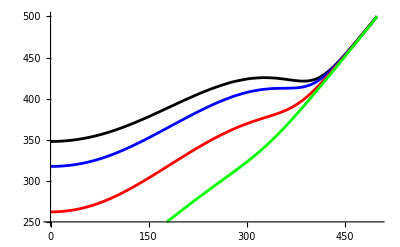

```mathematica
ListLinePlot[{ET1,ET100,ET130,ET150},PlotRange->{{0,500},{250,500}},PlotStyle->{Black,Blue,Red,Green}]
```